```mathematica
y1[x_]:=1+3x/2;
y2[y_]:=(1+3x/2)Log[(Sqrt[1+x]+1)/(Sqrt[1+x]-1)]-3*Sqrt[1+x];
```

```mathematica
y2''[x]+(2+3x)/2/x/(1+x)y2'[x]-3/2*y2[x]/x/(x+1)
```

(((3 x)/2+1) (√(x+1)-1) ((√(x+1)+1)/(4 (x+1)^(3/2) (√(x+1)-1)^2)+(√(x+1)+1)/(2 (x+1) (√(x+1)-1)^3)-1/(4 (x+1)^(3/2) (√(x+1)-1))-1/(2 (x+1) (√(x+1)-1)^2)))/(√(x+1)+1)+(((3 x)/2+1) (1/(2 √(x+1) (√(x+1)-1))-(√(x+1)+1)/(2 √(x+1) (√(x+1)-1)^2)))/(2 √(x+1) (√(x+1)+1))+(3 (√(x+1)-1) (1/(2 √(x+1) (√(x+1)-1))-(√(x+1)+1)/(2 √(x+1) (√(x+1)-1)^2)))/(√(x+1)+1)-(((3 x)/2+1) (√(x+1)-1) (1/(2 √(x+1) (√(x+1)-1))-(√(x+1)+1)/(2 √(x+1) (√(x+1)-1)^2)))/(2 √(x+1) (√(x+1)+1)^2)+3/(4 (x+1)^(3/2))+((3 x+2) ((((3 x)/2+1) (√(x+1)-1) (1/(2 √(x+1) (√(x+1)-1))-(√(x+1)+1)/(2 √(x+1) (√(x+1)-1)^2)))/(√(x+1)+1)-3/(2 √(x+1))+3/2 log((√(x+1)+1)/(√(x+1)-1))))/(2 x (x+1))-(3 (((3 x)/2+1) log((√(x+1)+1)/(√(x+1)-1))-3 √(x+1)))/(2 x (x+1))

```mathematica
Simplify[%6]
```

0

```mathematica
s1=NDSolve[{Y''[x]+(2.5+1.5*0.6825*Exp[3x])Y'[x]-3*0.6825*Exp[3x]*Y[x]==0,Y[-5]==1,Y'[-5]==0},Y[x],{x,-5,0},AccuracyGoal->15];
```

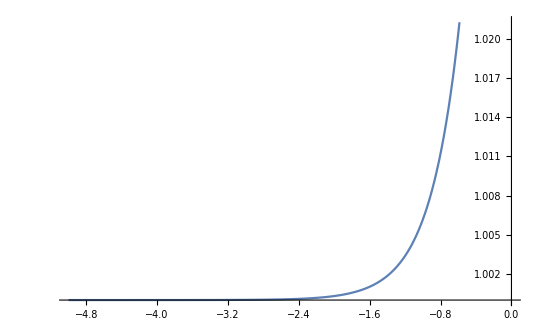

```mathematica
Plot[Evaluate[Y[x]/.s1],{x,-5,0}]
```

```mathematica
ini=7/3;
```

```mathematica
s1=NDSolve[{Y''[x]+(2.5+1.5*(ini*Exp[3x])/(ini*Exp[3x]+1))Y'[x]+3*(ini*Exp[3x])/(ini*Exp[3x]+1)*Y[x]==0,Y[-10]==1,Y'[-10]==0},Y[x],{x,-10,2},AccuracyGoal->15];
```

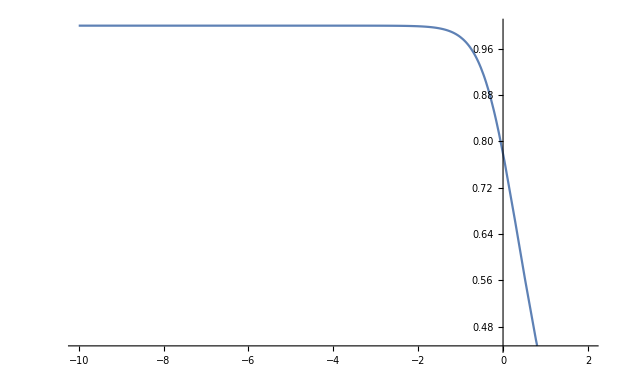

```mathematica
Plot[Evaluate[Y[x]/.s1],{x,-10,2}]
```